Abbe value & number of turning points

```mathematica
Abbe[data_]:=Abbe[data]=Length[data]/(2 (Length[data]-1)) Total[Differences[data]^2]/Total[(data-Mean[data])^2];
turn[data_]:=turn[data]=Total@Table[If[data[[i]]<data[[i+1]]>data[[i+2]],1,If[data[[i]]>data[[i+1]]<data[[i+2]],1,0]],{i,1,Length[data]-2}]
```

Example: fGn with H=0.75

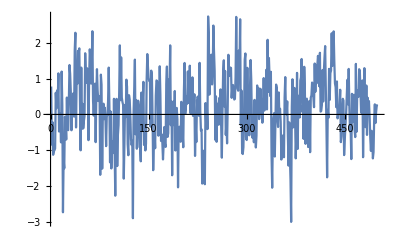

```mathematica
SeedRandom[1]
data=RandomFunction[FractionalGaussianNoiseProcess[0.75],{0,499,1}]["Path"][[All,2]];
ListLinePlot[data]
```

```mathematica
{Abbe[data],N@turn[data]/Length[data]}
```

{0.599137,0.628}

The theoretical values are [M. Tarnopolski, Physical Review E 100, 062144 (2019)]:

```mathematica
A[H_]:=2-2^(2 H-1)
```

```mathematica
T[H_]:=1-2/π ArcSin[1/2 Sqrt[(3^(2 H)-2^(2 H+1)-1)/(2^(2 H)-4)]]
```

```mathematica
{A[0.75],T[0.75]}
```

{0.585786,0.622909}

PLC in the 𝒜-𝒯 plane

noiseGenerator generates a time series of length 2×numberOFfreqComponents, from a PLC PSD with β=slope and Poisson noise level C=level. In the implementation below, the frequencies are constrained within the interval [10^-3.55,10^-1.15].

```mathematica
noiseGenerator[slope_,level_,numberOFfreqComponents_]:=
Block[{PSD,Xphase,freqs,Xampl,freqs2,Xcomplex,Xsim},
PSD[f_]:=1/(f+10^-18)^slope+level;
Xphase=RandomReal[{0,2 Pi},numberOFfreqComponents];
Xphase[[1]]=0;
Xphase[[-1]]=0;
freqs=Subdivide[10^-3.55,10^-1.15,numberOFfreqComponents/2-1];
Xampl=Sqrt[(PSD/@freqs)]~Join~Reverse[Sqrt[(PSD/@freqs)]];
freqs2=freqs~Join~Reverse[freqs];
Xcomplex=Xampl Exp[I Xphase];
Xsim=InverseFourier[Xcomplex]//Abs
]
```

```mathematica
noisesPL=Monitor[Table[ParallelTable[noiseGenerator[slope,0,2 499],100],{slope,0,3,0.1}],slope];//AbsoluteTiming
```

{5.35431,Null}

```mathematica
atPL=Table[{Mean@#,StandardDeviation@#}&@({Abbe[#],N@turn[#]/Length[#]}&/@noisesPL[[i]]),{i,1,Length@noisesPL}];//AbsoluteTiming
```

{2.89797,Null}

```mathematica
Needs["ErrorBarPlots`"]
```

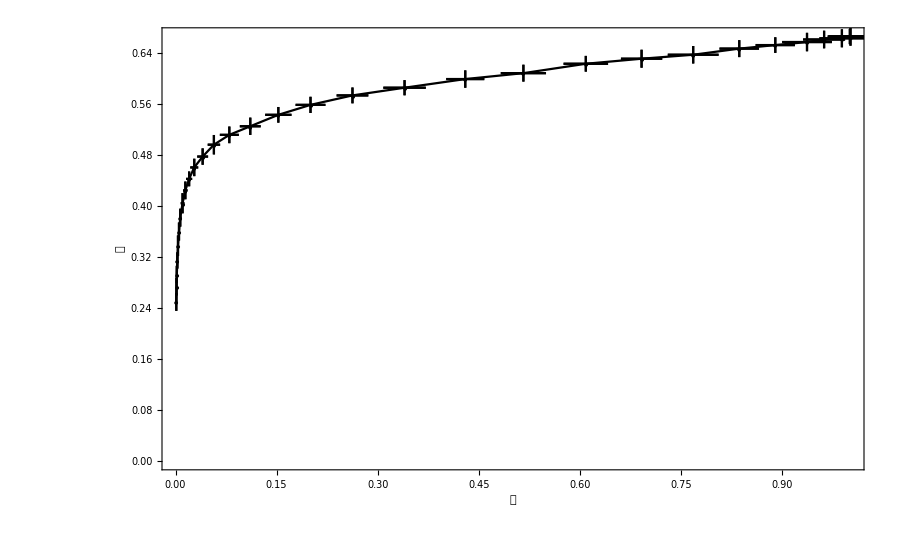

```mathematica
ErrorListPlot[Transpose[{atPL[[All,1]],ErrorBar@@@atPL[[All,2]]}],Frame->True,PlotRange->All,ImageSize->900,PlotStyle->Black,FrameStyle->Black,PlotMarkers->{Automatic,5},Joined->True,FrameLabel->{"𝒜",Rotate["𝒯",270 Degree]},BaseStyle->20]
```